```mathematica
(*generating hypsometry*)
```

```mathematica
hFiles=FileNames["output_steady/hini*"];
bedFiles=FileNames["bed/bed*"];
Ng=Length@bedFiles; 
idBt={{"rgiid","bt"}};
For[f=1,f≤Ng,f++,
bed=Import[bedFiles[[f]],"Table"][[;;,3]];
hb=Import[hFiles[[f]],"Table"][[;;,3;;4]];
bhb=Transpose@{bed,hb[[;;,1]],hb[[;;,2]]};
bhb=Select[bhb,#[[2]]>0&];
a=HistogramList[bhb[[;;,1]]+bhb[[;;,2]],{25}];
Export["./output_steady/hypso"<>StringTake[hFiles[[f]],-8],Transpose@{.5(a[[1,2;;]]+a[[1,1;;-2]]),a[[2,;;]]},"Table"];
AppendTo[idBt,{StringTake[hFiles[[f]],-8],Min@bhb[[;;,3]]}];
]
Export ["id_bt.txt",idBt,"Table"];
```

14.11547

{{4675,4700,4725,4750,4775,4800,4825,4850,4875,4900,4925,4950,4975,5000,5025,5050,5075,5100,5125,5150,5175,5200,5225,5250,5275,5300,5325,5350,5375,5400,5425,5450,5475,5500,5525,5550,5575,5600,5625,5650,5675,5700,5725,5750,5775,5800,5825},{2,9,3,9,6,5,4,7,6,5,5,4,7,9,10,11,11,14,13,10,12,17,15,16,14,20,10,10,8,13,10,13,8,6,6,4,7,3,4,5,3,5,0,3,2,2}}

{{4675,4700,4725,4750,4775,4800,4825,4850,4875,4900,4925,4950,4975,5000,5025,5050,5075,5100,5125,5150,5175,5200,5225,5250,5275,5300,5325,5350,5375,5400,5425,5450,5475,5500,5525,5550,5575,5600,5625,5650,5675,5700,5725,5750,5775,5800,5825},{2,9,3,9,6,5,4,7,6,5,5,4,7,9,10,11,11,14,13,10,12,17,15,16,14,20,10,10,8,13,10,13,8,6,6,4,7,3,4,5,3,5,0,3,2,2}}

tmp

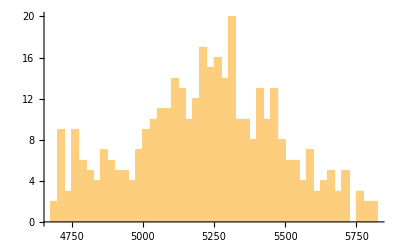

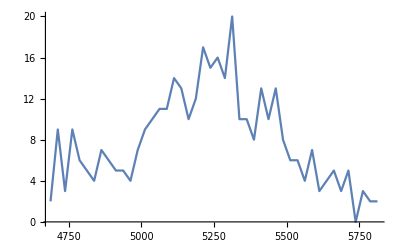

```mathematica
(*StringTake[hFiles[[1]],-8]
a=HistogramList[bhb[[;;,1]]+bhb[[;;,2]],{25}]
a
Export["tmp",Transpose@{.5(a[[1,2;;]]+a[[1,1;;-2]]),a[[2,;;]]},"Table"]
Histogram[bhb[[;;,1]]+bhb[[;;,2]],{25}]
ListPlot[Transpose@{.5(a[[1,2;;]]+a[[1,1;;-2]]),a[[2,;;]]}, PlotRange->All,Joined->True]
```

```mathematica
Select[z[[1;;10]],#>1&,Infinity]
```

{}

```mathematica
Threshold
```

Clip